```mathematica
NLODEs = {D[x[t],t] == V0 + V1 β - V2  + V3 + kf y[t] - k x[t],D[y[t],t]== V2 - V3 - kf y[t], D[z[t],t] ==  β V4 - V5 - ϵ z[t]}/.{V2->VM2 x[t]^2/(k2^2 + x[t]^2),V3-> VM3 x[t]^m/(kx^m + x[t]^m)y[t]^2/(ky^2 + y[t]^2)z[t]^4/(kz^4 + z[t]^4),V5->VM5 z[t]^p/(k5^p + z[t]^p)x[t]^n/(kd^n + x[t]^n)}
```

{x'[t]==V0+V1 β-k x[t]-(VM2 x[t]^2)/(k2^2+x[t]^2)+kf y[t]+(VM3 x[t]^m y[t]^2 z[t]^4)/((kx^m+x[t]^m) (ky^2+y[t]^2) (kz^4+z[t]^4)),y'[t]==(VM2 x[t]^2)/(k2^2+x[t]^2)-kf y[t]-(VM3 x[t]^m y[t]^2 z[t]^4)/((kx^m+x[t]^m) (ky^2+y[t]^2) (kz^4+z[t]^4)),z'[t]==V4 β-ϵ z[t]-(VM5 x[t]^n z[t]^p)/((kd^n+x[t]^n) (k5^p+z[t]^p))}

```mathematica
tmax = 20;
```

### Chaos

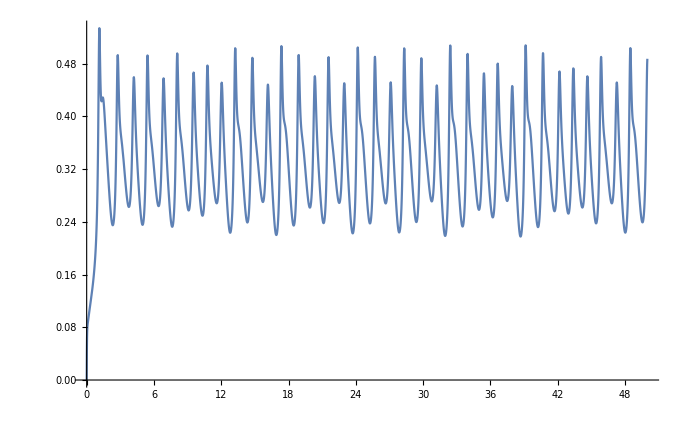

```mathematica
VvalsSS = {V0->2,V1->2 , V4->3, kf->1,k->10,β-> 0.65,ϵ->13 ,VM2->6,k2->0.1,VM3->30,m->2,kx->0.6,ky->0.3,kz->0.1,VM5->50,k5->0.3194,kd->1,p->1,n->4};
solSS1= NDSolve[Join[NLODEs/.VvalsSS,{x[0]==0,y[0]==0,z[0]==0}],{x[t],y[t],z[t]},{t,0,tmax}];
xv1 = x[t]/.solSS1;
Plot[xv1,{t,0,tmax},PlotRange->All]
```

```mathematica
ParametricPlot3D[{x[t]/.solSS1[[1]],y[t]/.solSS1[[1]],z[t]/.solSS1[[1]]},{t,0,tmax},AxesLabel->{"x","y","z"},PlotRange->{{0.2,0.6},{0.6,1.3},{0,0.15}}]
```

-Graphics3D-

### Period Doubling

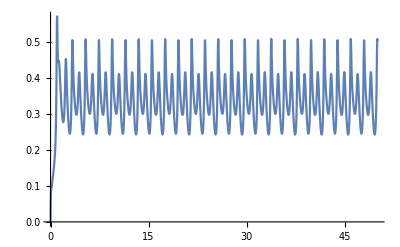

```mathematica
VvalsSS = {V0->2,V1->2 , V4->3, kf->1,k->10,β-> 0.7,ϵ->13 ,VM2->6,k2->0.1,VM3->30,m->2,kx->0.6,ky->0.3,kz->0.1,VM5->50,k5->0.3194,kd->1,p->1,n->4};
solSS1= NDSolve[Join[NLODEs/.VvalsSS,{x[0]==0,y[0]==0,z[0]==0}],{x[t],y[t],z[t]},{t,0,tmax}];
xv1 = x[t]/.solSS1;
Plot[xv1,{t,0,tmax},PlotRange->All]
```

```mathematica
ParametricPlot3D[{x[t]/.solSS1[[1]],y[t]/.solSS1[[1]],z[t]/.solSS1[[1]]},{t,10,tmax},AxesLabel->{"x","y","z"}(*,PlotRange->{{0.2,0.6},{0.6,1.3},{0,0.15}}*)]
```

-Graphics3D-

### Quasi-Periodic

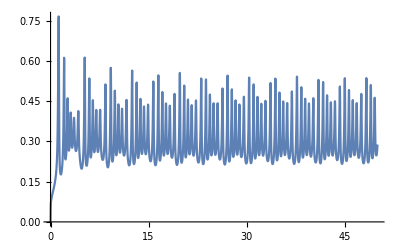

```mathematica
VvalsSS = {V0->2,V1->2 , V4->5, kf->1,k->10,β-> 0.51,ϵ->0.1 ,VM2->6,k2->0.1,VM3->20,m->2,kx->0.5,ky->0.2,kz->0.2,VM5->30,k5->0.3,kd->0.5,p->2,n->4};
solSS1= NDSolve[Join[NLODEs/.VvalsSS,{x[0]==0,y[0]==0,z[0]==0}],{x[t],y[t],z[t]},{t,0,tmax}];
xv1 = x[t]/.solSS1;
Plot[xv1,{t,0,tmax},PlotRange->All]
```

```mathematica
ParametricPlot3D[{x[t]/.solSS1[[1]],y[t]/.solSS1[[1]],z[t]/.solSS1[[1]]},{t,10,tmax},AxesLabel->{"x","y","z"}(*,PlotRange->{{0.2,0.6},{0.6,1.3},{0,0.15}}*)]
```

-Graphics3D-

### Birhythmicity

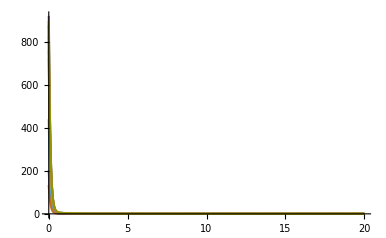

```mathematica
VvalsSS = {V0->2,V1->2 , V4->3, kf->1,k->10,β-> 0.52,ϵ->11 ,VM2->6,k2->0.1,VM3->30,m->2,kx->0.6,ky->0.3,kz->0.1,VM5->50,k5->0.3194,kd->1,p->1,n->4};
solSS1= Table[NDSolve[Join[NLODEs/.VvalsSS,{x[0]==RandomReal[{0,1000}],y[0]==RandomReal[{0,100}],z[0]==RandomReal[{0,100}]}],{x[t],y[t],z[t]},{t,0,tmax}],{i,1,10}];
xv1 = Table[x[t]/.solSS1[[nn]],{nn,1,10}];
Plot[xv1,{t,0,tmax},PlotRange->All]
```

```mathematica
tl1 = Table[{x[t]/.solSS1[[n1]],y[t]/.solSS1[[n1]],z[t]/.solSS1[[n1]]},{n1,1,10}];
```

```mathematica
Table[ParametricPlot3D[tl1[[m1]],{t,0,tmax},AxesLabel->{"x","y","z"}(*,PlotRange->{{0.2,0.6},{0.6,1.3},{0,0.15}}*)],{m1,1,10}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

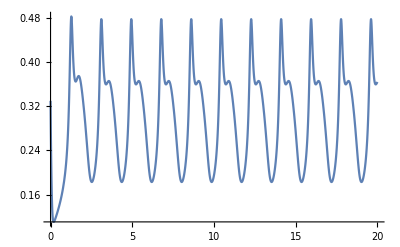

```mathematica
VvalsSS = {V0->2,V1->2 , V4->3, kf->1,k->10,β-> 0.52,ϵ->11 ,VM2->6,k2->0.1,VM3->30,m->2,kx->0.6,ky->0.3,kz->0.1,VM5->50,k5->0.3194,kd->1,p->1,n->4};
solSS1= NDSolve[Join[NLODEs/.VvalsSS,{x[0]==0.330,y[0]==0.2,z[0]==0.2}],{x[t],y[t],z[t]},{t,0,tmax}];
xv1 = x[t]/.solSS1;
Plot[xv1,{t,0,tmax},PlotRange->All]
```

```mathematica
ParametricPlot3D[{x[t]/.solSS1[[1]],y[t]/.solSS1[[1]],z[t]/.solSS1[[1]]},{t,10,tmax},AxesLabel->{"x","y","z"}(*,PlotRange->{{0.2,0.6},{0.6,1.3},{0,0.15}}*)]
```

-Graphics3D-